# 4T Modelling Thermodynamics and Equilibrium of mixture of radiation field, ionic gas and electron gas

## Constants and Functions

electron-ion collision cross sections
typically 10^(-11) m^2
https://www.nist.gov/system/files/documents/srd/jpcrd386.pdf

```mathematica
(* Initial parameters and constants *)

c = 3.0*10^(8)
ep0 = 8.8541878128*10^(−12);
kb = 1.380649*10^(−23);
ee = 1.602*10^(-19);
na=6.02*10^23; (* avogadros number*)

a = 2*10^(-10);
mp = 1.67262192*10^(-27);
md = 2.014102*mp;(*mass deuterium*)
mt= 3.016049*mp;(*mass tritium*)
mal = 4.002603*mp; (**)
hbar = 1.05457182 *10^(-34);
me = 9.1093837*10^(-31);
mme=me*na; (* molar electron mass*)
ui = 13.6 * ee;(* ionization energy for hydrogen*)

ar = 5.670374*10^(-8) ;(* stefan-boltzmann constant *)

sigmaie = 1.0*10^(-11); (* e- ion collision cross section  m^2*)
sigmaii  = Pi*a*a; (* ion ion collision cross section based on atomic size *)

(*Nuclear Constants for burning and transfer*)
sigt= (8/Pi)*(ee^2/(me*c*c))^2;  (*thompson cross section*)
```

3.×10^8

## Model Parameters

```mathematica
(*The model parameters*)
Ni=1; (* number of moles of ions in total*)
ni0 = 1.0; (*initial number of moles of ions*)
ne=Ni;  (* number of electrons*)
```

```mathematica
(* Saha equation*) (* Here calculate the ionization fraction *)
x[N_,T_, Ne_]:= ((2*Pi*me*kb/hbar)^(3/2))*(T^(3/2)/Ne)*Exp[-(ui/(kb*T))]; (* Ne is electron number density *) (* typical ne 10^(-20)*)

(* time between collisions ... relaxation time*)
taun[N_,T_]:=(1/(N*sigmaii))*Sqrt[mp/(kb*T)];
taue[Ne_,Te_]:=(1/(Ne*sigmaie))*Sqrt[me/(kb*Te)]
```

## Radiation and Perfect Gas

and Gas Perfect Radiation

```mathematica
pr[N_, Vo_, T_]:= (N*kb*T/Vo)+(ar*T^4)/3;
Et[N_,Vo_,T_]:= (3/2)*(N*kb*T)+(Vo*ar*T^4);
St[N_,Vo_,T_]:= N*kb*Log[Vo*T^(3/2)]+(4/3)*ar*Vo*T^3
```

## Radiation and Ionic Gas

```mathematica
(*   using saha equation  to get energy and pressure for ionic gas and radiation field*)
```

## Planck and Bose Einstein Distribution

```mathematica
(*  Planck distribution*)
```

```mathematica
npl[nu_,T_]:= 1.0/(Exp[2*Pi*hbar*nu/(kb*T)]-1.0)
```

```mathematica
(* Bose-Einstein distribution*)
```

```mathematica
nbe[nu_,mu_,T_]:= 1.0/(Exp[((2*Pi*hbar*nu)/(kb*T))-mu]-1.0)
```

```mathematica
fbe[ep_,al_]:= 1.0/(Exp[ep+al]-1.0);
```

## Rates for Nuclear Reactions

```mathematica
(* rates for nuclear reactions*)
```

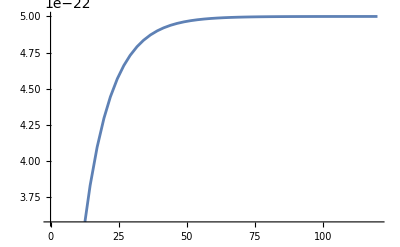

```mathematica
Adt=5.0*10^(-22); (* m^3/s*)
kdt=0.1;
T0dt=1.0;
sigvdt[T_]:=Adt*(T0dt-Exp[-kdt*T]);(*DT fusion reaction cross section sigv*) (*T is the temperature in keV*)
Plot[sigvdt[x1],{x1,0,120}]
```

```mathematica
(* functions *)
nuc[ne_] := c*sigt*ne(* compton strength*);
lambda[te_,ne_]:= 25.127-Log[(ne^0.5)/(1000.0*te)];
fali[te_]:= te/(te+32);

(*mme molar mass of electron*)
pei[ne_, ni_,nal_,te_,ti_]:=(6/Sqrt[Pi])*nuc[ne]*ni*((mme/md)+(mme/mt)+4*((ni0-ni)/ni)*(mme/mal))*((me*c*c/(2*te))^(3/2))*Log[lambda[te,ne]]*(ti-te);
```

## Experiments

```mathematica
2*Pi*hbar/kb
```

4.79924×10^-11

3.×10^17

{1./(-1.+ⅇ^(-0.005+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.1+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.2+(1.43977×10^7)/T)),1./(-1.+ⅇ^(-0.3+(1.43977×10^7)/T))}

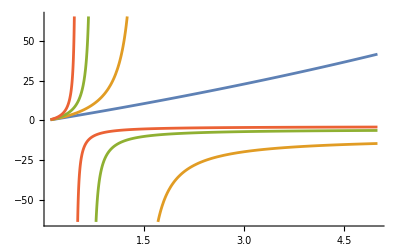

```mathematica
nur = 3.0*10^(17)
myl={nbe[nur,0.005,T], nbe[nur,0.1,T]   ,   nbe[nur,0.2,T] ,   nbe[nur,0.3,T]}
Plot[myl,{T,10*10^6,500*10^6}]
```

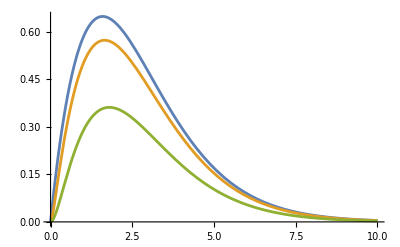

```mathematica
Plot[{x1^2*fbe[x1,0],x1^2*fbe[x1,0.1],x1^2*fbe[x1,0.5]},{x1,0,10}]
```

```mathematica
A=2;
k=1;
x0=1.0;
```

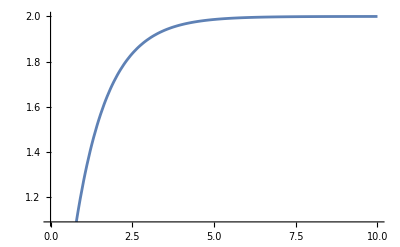

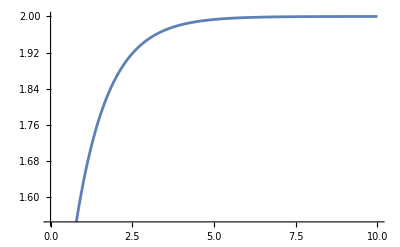

```mathematica
y1[x_]:=A*(x0-Exp[-k*x]);
Plot[y1[x1],{x1,0,10}]
```